# Recursion

## Do loops and recursive functions

## Do loops

Counting from 1 to 10

```mathematica
Do[Print[i], {i, 1, 5}]
```

1

2

3

4

5

```mathematica
Do[Print[i], {i, 0, 2, 0.5}]
```

0.

0.5

1.

1.5

2.

### Performing a summation

```mathematica
s = 0;
Do[s = s + 1, {i, 1, 20}]
s
```

20

Summing all numbers from 1 to 10

```mathematica
s = 0;
Do[s = s + i, {i, 1, 10}]
s
```

55

### Working with analytical summations

Slower since we are working with symbols

```mathematica
∑_(n=1)^N n^2
```

1/6 N (1+N) (1+2 N)

### Vectors

```mathematica
v = Range[2, 8];
s= 0;
Do[s = s + v[[i]], {i, 1, Length[v]}]
s
```

35

## While loops

When we do not know how many time will we iterate over a function

```mathematica
x=0;
While[x < 5, Print[x]; x ++]
```

0

1

2

3

4

### Some examples

Creating a matrix of ones

```mathematica
M = Array[Subscript[α, ##] &, {3, 3}];
M // MatrixForm
```

(α_(1,1) | α_(1,2) | α_(1,3)
α_(2,1) | α_(2,2) | α_(2,3)
α_(3,1) | α_(3,2) | α_(3,3))

```mathematica
Do[Subscript[α, i,j] =  i * j, {j, 1, 3}, {i, 1, 3}]
M //MatrixForm
```

(1 | 2 | 3
2 | 4 | 6
3 | 6 | 9)

Creating the factorial function
With recursion

```mathematica
factorial[k_]:= If[k == 1,  1, k * factorial[k - 1]]
factorial[5]
```

120

Recursion to sum a series of numbers

```mathematica
sumSeries[m_] := If[m == 0, 0, m + sumSeries[m - 1]]
sumSeries[5]
```

15

```mathematica
∑_(t=0)^15 t
```

120

The Fibonacci sequence

```mathematica
fibonacci[n_] := Which[n == 0, 0, n ==1, 1, n ≥ 2,
Fibonacci[n-1]+ Fibonacci[n - 2]
]
```

Our version

```mathematica
fibonacci[30]
```

832040

Mathematica’s version

```mathematica
Fibonacci[30]
```

832040

### A final plot

```mathematica
PlotRange[Fibonacci[x] / Fibonacci[x-1], {x, 2, 10}]
```

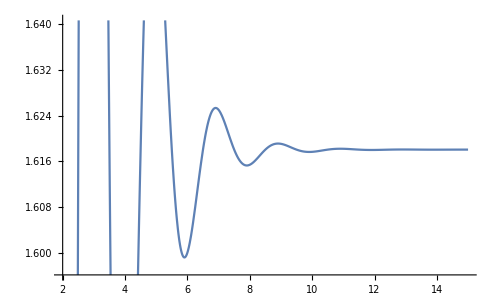

```mathematica
Plot[Fibonacci[x]/Fibonacci[-1+x],{x,2,15}]
```